## Solving Catalysis Problem using Interpolation

Parameters

```mathematica
m=2;
alphaP=1;
alphaS=1;
beta=1;
r0=0.0001;
```

### Particle Problem

Find C0starMax such that Cp(1) is slightly greater than 1

```mathematica
solcp[C0star_]:=NDSolve[{D[r^2 P[r],r]==alphaP^2 r^2 Cp[r]^m,Cp'[r]==P[r],Cp[r0]==C0star+r0^2/6 alphaP^2 C0star^m,P[r0]==(r0)/3 alphaP^2 C0star^m},{Cp[r],P[r]},{r,r0,1}]
```

```mathematica
C0starMax=0.87;
{Cp[r]/.solcp[C0starMax]/.r->1}[[1]][[1]]
```

1.00802

Choose scale such that the data is evenly spaced in the plot

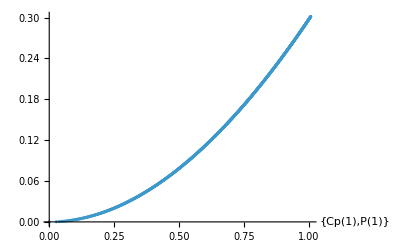

```mathematica
scale=0.5;
ketab=Table[{{Cp[r]/.solcp[(0.001i)^scale*C0starMax]/.r->1}[[1]][[1]],{P[r]/.solcp[(0.001*i)^scale*C0starMax]/.r->1}[[1]][[1]]},{i,0,1000}];
ListPlot[ketab, AxesLabel->{{"Cp(1)","P(1)"}}]
ke=Interpolation[ketab];
```

### Membrane Problem

```mathematica
solcs[i_]:=NDSolve[{Cs'[z]==S[z],S'[z]==alphaS^2*ke[Cs[z]],Cs[0]==i,S[1]==0},{Cs,S},z,Method->{"Shooting","StartingInitialConditions"->{Cs[0]==i,S[0]==-2Sqrt[alphaP/(m+3)](2/(m+1))^0.25alphaS*i^((m+3)/4)}}]
```

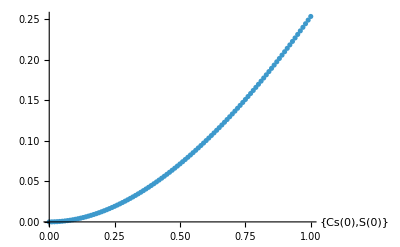

```mathematica
kstab=Table[{{Cs[z]/.solcs[0.01i]/.z->0}[[1]][[1]],{-S[z]/.solcs[0.01i]/.z->0}[[1]][[1]]},{i,0,100}];
ListPlot[kstab, AxesLabel->{{"Cs(0)","S(0)"}}]
ks=Interpolation[kstab];
```

### Channel Problem

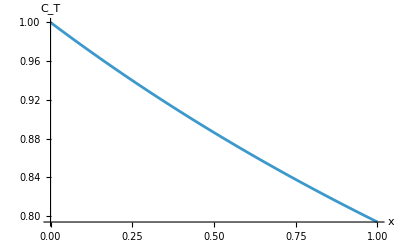

C_out=0.793992

```mathematica
solct=NDSolve[{Ct'[x]==-beta*ks[Ct[x]],Ct[0]==1},Ct[x],{x,0,1}];
Plot[Ct[x]/.solct,{x,0,1},AxesLabel->{"x",Subscript["C","T"]}]
Cout={Ct[x]/.solct/.x->1}[[1]][[1]];
Print[Subscript["C","out"],"=",Cout]
```